# Prueba Mec. Intermedia

#### Particula sin roce

```mathematica
cylinderPlot3D[f_,{rMin_,rMax_},{tMin_,tMax_},opts___]:=ParametricPlot3D[{r Cos[t],r Sin[t],f[r,t]},{r,rMin,rMax},{t,tMin,tMax},opts];
z[r_,t_]:=Sin[r];
cylinderPlot3D[z,{0,Pi/2},{0,2 Pi},Mesh->None,Boxed->False,ColorFunction->"Rainbow"]
```

-Graphics3D-

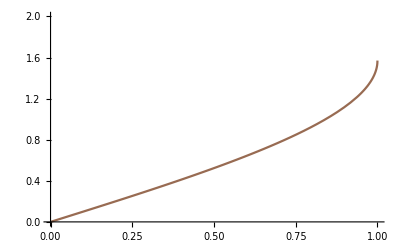

```mathematica
Plot[ArcSin[x],{x,0,1},PlotRange->{0,2},ColorFunction->"DarkRainbow"]
```

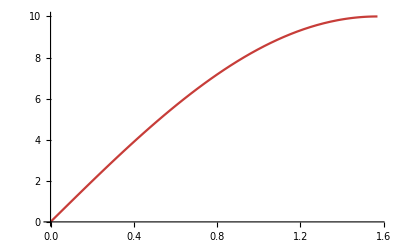

```mathematica
R=10;
g=9.81;
Plot[R Sin[x],{x,0,Pi/2},ColorFunction->"Rainbow"]
```

No se observa con claridad o me cabe donde puede existir una orbita horizontal establa, se descartara la posible solucion que podia o no entregar esta parte (tiene que ver con el desarrollo en hoja, es solo visualizacion)